# KIE of non-adiabatic PCET

All rate expressions

## Constants

### Unit conversions

```mathematica
bohr2a=0.529177;
a2bohr=1/bohr2a;
```

```mathematica
au2kcal=627.5095;
kcal2au=1/au2kcal;
```

```mathematica
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
```

### Universal constants

```mathematica
ℏ=1;
hbarps=0.047685388/(au2kcal π);
```

```mathematica
Dalton=1822.8880;
```

```mathematica
μH=1836.1526675;
```

```mathematica
μD=3670.4829550;
```

```mathematica
kb=3.16683 10^-6;
```

### Accuracy settings

```mathematica
AccN=100;
```

## Morse potentials for D-H (reactant) and A-H (product) bonds

### Proton transfer interface geometry

```mathematica
RCH=1.09;
ROH=0.96;
```

Distance between minima of reactant and product potential energy curves

```mathematica
R0[RDA_]:=(RDA-RCH-ROH)a2bohr;
```

### Morse parameters (1 - reactant; 2 - product)

```mathematica
D1=77/au2kcal;
β1=2.068 bohr2a;
Print["Reactant proton vibrational frequency: ",Panel[au2cm β1 √((2D1)/μH)]," cm^-1"];
Print["Reactant deuteron vibrational frequency: ",Panel[au2cm β1 √((2D1)/μD)]," cm^-1"];
```

Reactant proton vibrational frequency: 2776.71 cm^-1

Reactant deuteron vibrational frequency: 1963.92 cm^-1

```mathematica
D2=82/au2kcal;
β2=2.442 bohr2a;
Print["Product proton vibrational frequency: ",Panel[au2cm β2 √((2D2)/μH)]," cm^-1"];
Print["Product deuteron vibrational frequency: ",Panel[au2cm β2 √((2D2)/μD)]," cm^-1"];
```

Product proton vibrational frequency: 3383.66 cm^-1

Product deuteron vibrational frequency: 2393.2 cm^-1

Morse potentials (equlibrium position at x=0):

```mathematica
U1[x_]:=D1(1-Exp[-β1 x])^2;
U2[x_]:=D2(1-Exp[-β2 x])^2;
```

```mathematica
Manipulate[Plot[{U1[x+R0[d]/2]au2kcal,U2[-x+R0[d]/2]au2kcal},{x,-2,2},PlotRange->{-5,100},PlotStyle->{Blue,Red},Axes->False,Frame->True,FrameLabel->{"Proton coordinate (Bohr)"}],{{d,3,"Donor-acceptor distance (A)"},2,4},FrameLabel->{None,None,Style[Framed["Reactant and product Morse potentials",FrameMargins->12,ImageMargins->20],Blue]}]
```

## Harmonic potentials for D-H (reactant) and A-H (product) bonds

Frequencies:

```mathematica
ω1H=β1 √((2D1)/μH);
ω2H=β2 √((2D2)/μH);
ω1D=β1 √((2D1)/μD);
ω2D=β2 √((2D2)/μD);
```

Harmonic potentials (equlibrium position at x=0):

```mathematica
Uharm1[x_]:=β1^2 D1 x^2;
Uharm2[x_]:=β2^2 D2 x^2;
```

```mathematica
Manipulate[Plot[{Uharm1[x+R0[d]/2]au2kcal,Uharm2[-x+R0[d]/2]au2kcal},{x,-2,2},PlotRange->{-5,100},PlotStyle->{Blue,Red},Axes->False,Frame->True,FrameLabel->{"Proton coordinate (Bohr)"}],{{d,3,"Donor-acceptor distance (A)"},2,4},FrameLabel->{None,None,Style[Framed["Reactant and product harmonic potentials",FrameMargins->12,ImageMargins->20],Blue]}]
```

## Analytical expressions for harmonic oscillator energies and wavefunctions

Energies:

```mathematica
ϵ1[i_]:=SetAccuracy[ℏ ω1H(i+1/2),AccN];
ϵ2[i_]:=SetAccuracy[ℏ ω2H(i+1/2),AccN];
ϵ1D[i_]:=SetAccuracy[ℏ ω1D(i+1/2),AccN];
ϵ2D[i_]:=SetAccuracy[ℏ ω2D(i+1/2),AccN];
```

Wavefunctions:

```mathematica
ψ1[x_,n_]:=((μH ω1H)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(μH ω1H)/(2ℏ) x^2]HermiteH[n,x √((μH ω1H)/ℏ)];
ψ1D[x_,n_]:=((μD ω1D)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(μD ω1D)/(2ℏ) x^2]HermiteH[n,x √((μD ω1D)/ℏ)];
ψ2[x_,n_]:=((μH ω2H)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(μH ω2H)/(2ℏ) x^2]HermiteH[n,x √((μH ω2H)/ℏ)];
ψ2D[x_,n_]:=((μD ω2D)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(μD ω2D)/(2ℏ) x^2]HermiteH[n,x √((μD ω2D)/ℏ)];
```

```mathematica
Manipulate[Plot[{Uharm1[x+R0[d]/2]au2kcal,Uharm2[-x+R0[d]/2]au2kcal,au2kcal/40 ψ1[x+R0[d]/2,i]^2+ϵ1[i]au2kcal,au2kcal/40 ψ2[-x+R0[d]/2,j]^2+ϵ2[j]au2kcal},{x,-2,2},PlotRange->{-20,100},Frame->True,Axes->False,FrameLabel->{"Proton coordinate (Bohr)"},PlotStyle->{Blue,Red,Blue,Red},Filling->{3->ϵ1[i]au2kcal,4->ϵ2[j]au2kcal},FillingStyle->{3->Blue,4->Red}],{{d,2.7,"Donor-acceptor distance (A)"},2,4},{{i,0,"Reactant state"},0,10,1},{{j,0,"Product state"},0,10,1},FrameLabel->{None,None,Style[Framed["Reactant and product squared wavefunctions",FrameMargins->12,ImageMargins->20],Blue]}]
```

Filling::invfillentry: 627.51\ ϵ1[0] is not a valid Filling specification.

Filling::invfillentry: 627.51\ ϵ2[0] is not a valid Filling specification.

## Analytical expressions for the Morse wavefunctions from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] (typo in Eq.(38): factor √α is missing)

```mathematica
λ1=SetAccuracy[(√(2μH D1))/(β1 ℏ),AccN];
```

```mathematica
λ1D=SetAccuracy[(√(2μD D1))/(β1 ℏ),AccN];
```

```mathematica
λ2=SetAccuracy[(√(2μH D2))/(β2 ℏ),AccN];
```

```mathematica
λ2D=SetAccuracy[(√(2μD D2))/(β2 ℏ),AccN];
```

```mathematica
ξ1[x_]:=SetAccuracy[2λ1 Exp[-β1 x],AccN];
```

```mathematica
ξ1D[x_]:=SetAccuracy[2λ1D Exp[-β1 x],AccN];
```

```mathematica
ξ2[x_]:=SetAccuracy[2λ2 Exp[-β2 x],AccN];
```

```mathematica
ξ2D[x_]:=SetAccuracy[2λ2D Exp[-β2 x],AccN];
```

```mathematica
E1[n_]:=SetAccuracy[((n+1/2)-1/(2λ1)(n+1/2)^2)ℏ √((2D1 β1^2)/μH),AccN];
```

```mathematica
E1D[n_]:=SetAccuracy[((n+1/2)-1/(2λ1D)(n+1/2)^2)ℏ √((2D1 β1^2)/μD),AccN];
```

```mathematica
E2[n_]:=SetAccuracy[((n+1/2)-1/(2λ2)(n+1/2)^2)ℏ √((2D2 β2^2)/μH),AccN];
```

```mathematica
E2D[n_]:=SetAccuracy[((n+1/2)-1/(2λ2D)(n+1/2)^2)ℏ √((2D2 β2^2)/μD),AccN];
```

```mathematica
N1D[n_]:=SetAccuracy[√((β1(2λ1D-2n-1)Gamma[n+1])/Gamma[2λ1D-n]),AccN];
```

```mathematica
N2D[n_]:=SetAccuracy[√((β2(2λ2D-2n-1)Gamma[n+1])/Gamma[2λ2D-n]),AccN];
```

```mathematica
N1[n_]:=SetAccuracy[√((β1(2λ1-2n-1)Gamma[n+1])/Gamma[2λ1-n]),AccN];
```

```mathematica
N2[n_]:=SetAccuracy[√((β2(2λ2-2n-1)Gamma[n+1])/Gamma[2λ2-n]),AccN];
```

```mathematica
ϕ1[x_,n_]:=SetAccuracy[N1[n]Exp[-ξ1[x]/2] ξ1[x]^(λ1-n-1/2)LaguerreL[n,2λ1-2n-1,ξ1[x]],AccN];
```

```mathematica
ϕ1D[x_,n_]:=SetAccuracy[N1D[n]Exp[-ξ1D[x]/2] ξ1D[x]^(λ1D-n-1/2)LaguerreL[n,2λ1D-2n-1,ξ1D[x]],AccN];
```

```mathematica
ϕ2[x_,n_]:=SetAccuracy[N2[n]Exp[-ξ2[x]/2] ξ2[x]^(λ2-n-1/2)LaguerreL[n,2λ2-2n-1,ξ2[x]],AccN];
```

```mathematica
ϕ2D[x_,n_]:=SetAccuracy[N2D[n]Exp[-ξ2D[x]/2] ξ2D[x]^(λ2D-n-1/2)LaguerreL[n,2λ2D-2n-1,ξ2D[x]],AccN];
```

Number of bound states:

```mathematica
Nbound1=IntegerPart[λ1-1/2];
Nbound2=IntegerPart[λ2-1/2];
Nbound1D=IntegerPart[λ1D-1/2];
Nbound2D=IntegerPart[λ2D-1/2];
```

```mathematica
Nbound=Min[Nbound1,Nbound2,Nbound1D,Nbound2D]
```

16

Check sanity of the wavefunctions:

```mathematica
Manipulate[Plot[{U1[x+R0[d]/2]au2kcal,U2[-x+R0[d]/2]au2kcal,au2kcal/40 ϕ1[x+R0[d]/2,i]^2+E1[i]au2kcal,au2kcal/40 ϕ2[-x+R0[d]/2,j]^2+E2[j]au2kcal},{x,-2,2},PlotRange->{-20,100},Frame->True,Axes->False,FrameLabel->{"Proton coordinate (Bohr)"},PlotStyle->{Blue,Red,Blue,Red},Filling->{3->E1[i]au2kcal,4->E2[j]au2kcal},FillingStyle->{3->Blue,4->Red}],{{d,3,"Donor-acceptor distance (A)"},2,4},{{i,0,"Reactant state"},0,10,1},{{j,0,"Product state"},0,10,1},FrameLabel->{None,None,Style[Framed["Reactant and product squared wavefunctions",FrameMargins->12,ImageMargins->20],Blue]}]
```

```mathematica
Manipulate[Plot[{ϕ1[x+R0[d]/2,i],ϕ2[-x+R0[d]/2,j]},{x,-4,4},PlotRange->{-1.75,1.75},Frame->True,Axes->False,FrameLabel->{"Proton coordinate (Bohr)"},PlotStyle->{Blue,Red},Filling->{1->Axis,2->Axis},FillingStyle->{1->Blue,2->Red}],{{d,3,"Donor-acceptor distance (A)"},2,5,0.1},{{i,0,"Reactant state"},0,Nbound1,1},{{j,0,"Product state"},0,Nbound2,1},FrameLabel->{None,None,Style[Framed["Wavefunction overlap",FrameMargins->12,ImageMargins->20],Blue]}]
```

## Harmonic overlap integrals [J.-L. Chang, J. Mol. Spectrosc. 232 (2005) 102-104]

```mathematica
σH[R_,n_,m_]:=Module[{K,α1,α2,s,A,Prefactor,b1,b2,i,j},
α1=(μH ω1H)/ℏ;
α2=(μH ω2H)/ℏ;
s=(α1 α2 R^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
K[i_,j_]:=If[OddQ[i+j],0,((i+j-1)!!)/(α1+α2)^((i+j)/2)];
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(R α2 √α1)/(α1+α2);
b2=(R α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j]))

];
```

```mathematica
σD[R_,n_,m_]:=Module[{K,α1,α2,s,A,Prefactor,b1,b2,i,j},
α1=(μD ω1D)/ℏ;
α2=(μD ω2D)/ℏ;
s=(α1 α2 R^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
K[i_,j_]:=If[OddQ[i+j],0,((i+j-1)!!)/(α1+α2)^((i+j)/2)];
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(R α2 √α1)/(α1+α2);
b2=(R α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j]))

];
```

```mathematica
Manipulate[Plot[{Tooltip[-Log[Abs[σH[x,i,j]]],"σH("<>ToString[i]<>"-"<>ToString[j]<>")"],Tooltip[-Log[Abs[σD[x,i,j]]],"σD("<>ToString[i]<>"-"<>ToString[j]<>")"]},{x,0,2.5},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"Distance between minima (Bohr)"},PlotStyle->{Blue,{Blue,Dashed}},GridLines->{{{R0[d],Red}},{0}}],{{d,2.7,"Equilibrium distance (A)"},2.5,3.3,0.1},{{i,0,"Reactant state"},0,15,1},{{j,0,"Product state"},0,15,1},FrameLabel->{None,None,Style[Framed["R-dependence of harmonic overlaps",FrameMargins->12,ImageMargins->20],Blue]}]
```

```mathematica
αharmH[R_,i_,j_]:=Module[{x},
-1/σH[R,i,j]*D[σH[x,i,j],x]/.x->R];
αharmD[R_,i_,j_]:=Module[{x},
-1/σD[R,i,j]*D[σD[x,i,j],x]/.x->R];
```

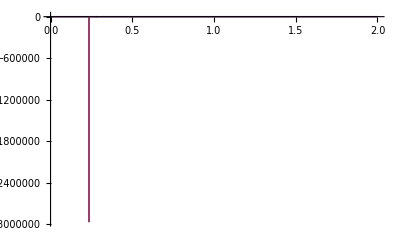

```mathematica
Plot[{αharmH[x,1,1],αharmD[x,1,1]},{x,0,2},PlotRange->All]
```

```mathematica
αharmH[0.2,1,1.2]
```

7.79032

## Morse overlap integrals in terms of the Wigner function based on [J. C. Lopez, A. L. Rivera, Yu. F. Smirnov, A. Frank, arXiv:physics/0109017v]

General case:

```mathematica
FCH[R_,nu1_,nu2_]:=
Module[{Acc,AccN,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=100;
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)(* Integration Section *)
(* Integral Ia.Calculation with scaling *)(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`100;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Fcsum];
```

```mathematica
FCD[R_,nu1_,nu2_]:=
Module[{Acc,AccN,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*---------------------------------------------------------------------*)(*This program computes the Franck-Condon factor of two Morse functions*)(*Usage:*)(*FCH[j1,nu1,beta1,R1,j2,nu2,beta2,R2,flag]*)(*flag=0 computes the FC factor*)
(*flag=1 computes the square of the FC factor*)(*---------------------------------------------------------------------*)(*Definition of Local Variables*)
Acc=15;
AccN=100;
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)(*Integration Section.Integral Ia.Calculation with scaling*)(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(*Integrand*)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`100;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Fcsum];
```

Case β_1=β_2:

```mathematica
FC0H[R_,nu1_,nu2_]:=
Module[{AccN,l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)
(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCH instead..."];Abort[])];
(* Accuracies: *)
AccN=100;
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

```mathematica
FC0D[R_,nu1_,nu2_]:=
Module[{AccN,l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCD instead..."];Abort[])];
(* Accuracies: *)
AccN=100;
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

## Morse overlap integrals and their distance dependence

```mathematica
SH[R_,i_,j_]:=Module[{x,integrand},
integrand=ϕ1[x,i]ϕ2[-x+R,j];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False,WorkingPrecision->40]];
```

```mathematica
Grid[{{N[SH[5,2,10],15]//Timing},{N[FCH[5,2,10],15]//Timing}}]
```

{0.453996,4.61729965756128×10^-8}
{0.621395,4.61729965756127×10^-8}

```mathematica
SD[R_,i_,j_]:=Module[{x,integrand},
integrand=ϕ1D[x,i]ϕ2D[-x+R,j];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False,WorkingPrecision->40]];
```

```mathematica
αH[R_,i_,j_]:=Module[{h},
h=0.0001;
SetAccuracy[-1/(2h)(Log[SH[R+h,i,j]]-Log[SH[R-h,i,j]]),AccN]];
```

```mathematica
αD[R_,i_,j_]:=Module[{h},
h=0.0001;
SetAccuracy[-1/(2h)(Log[SD[R+h,i,j]]-Log[SD[R-h,i,j]]),AccN]];
```

```mathematica
αH[1,1,1]
```

5.5536943292868397037409522454254329204559326171875

Coupling lengths for 0-0 overlap at equilibrium distance:

```mathematica
α0H[R_]:=αH[R,0,0];
α0D[R_]:=αD[R,0,0];
```

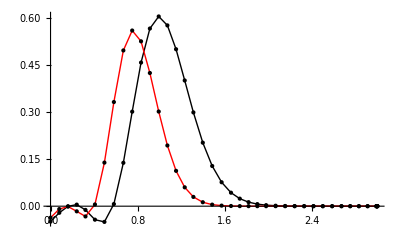

```mathematica
Plot[{Tooltip[SH[x,0,5],"SH(0-5)"],Tooltip[SD[x,0,5],"SD(0-5)"]},{x,0,3},PlotRange->All,PlotStyle->{Black,Red},MaxRecursion->2,Mesh->All,PlotPoints->10]
```

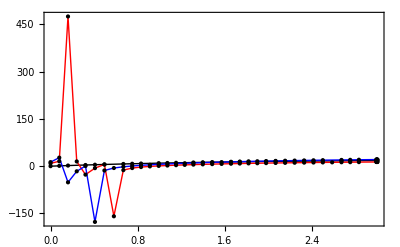

```mathematica
Plot[{Tooltip[αH[x,0,0],"αH(0-0)"],Tooltip[αH[x,0,5],"αH(0-5)"],Tooltip[αD[x,0,5],"αD(0-5)"]},{x,0,3},PlotStyle->{Black,Red,Blue},PlotRange->All,MaxRecursion->2,Mesh->All,PlotPoints->10,MeshStyle->{Black},Frame->True,Axes->False]
```

```mathematica
R0[2.7]
```

1.22832

## Partition function and Boltzmann factors

```mathematica
ZCH[T_,n_]:=Module[{i},SetAccuracy[1+Sum[Exp[-(E1[i]-E1[0])/(kb T)],{i,1,n}],AccN]];
```

```mathematica
ZCD[T_,n_]:=Module[{i},SetAccuracy[1+Sum[Exp[-(E1D[i]-E1D[0])/(kb T)],{i,1,n}],AccN]];
```

```mathematica
PCH=Function[{T,i,n},SetAccuracy[1/ZCH[T,n] Exp[-(E1[i]-E1[0])/(kb T)],AccN]];
```

```mathematica
PCD=Function[{T,i,n},SetAccuracy[1/ZCD[T,n] Exp[-(E1D[i]-E1D[0])/(kb T)],AccN]];
```

## Time Correlation Functions

#### Classical

```mathematica
CRC0=Function[{T,μ,ω},SetAccuracy[(kb T)/(μ Dalton (ω cm2au)^2),AccN]];
```

```mathematica
CRC=Function[{T,μ,ω,t},SetAccuracy[(kb T)/(μ Dalton (ω cm2au)^2)Cos[ω cm2au t],AccN]];
```

#### Quantum

```mathematica
CRQ0=Function[{T,μ,ω},SetAccuracy[ℏ/(2μ Dalton ω cm2au)Coth[(ω cm2au)/(2kb T)],AccN]];
```

```mathematica
CRQ=Function[{T,μ,ω,t},SetAccuracy[ℏ^2/(2μ Dalton ω cm2au)(Coth[(ω cm2au)/(2kb T)]Cos[(ω cm2au)/ℏ t]+ⅈ Sin[(ω cm2au)/ℏ t]),AccN]];
```

## Flux expressions (harmonic R-mode, short-time approximation)

```mathematica
λaH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 αH[R,i,j]^2)/(2μ Dalton),AccN]];
```

```mathematica
λaD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 αD[R,i,j]^2)/(2μ Dalton),AccN]];
```

```mathematica
λa0H=Function[{R,μ},SetAccuracy[(ℏ^2 α0H[R]^2)/(2μ Dalton),AccN]];
```

```mathematica
λa0D=Function[{R,μ},SetAccuracy[(ℏ^2 α0D[R]^2)/(2μ Dalton),AccN]];
```

```mathematica
V=SetAccuracy[1.0/au2kcal,AccN];
```

```mathematica
prefactor=SetAccuracy[10^12/au2ps,AccN];
```

Solvent damping term:

```mathematica
Sterm[λ_,T_,t_]:=SetAccuracy[Exp[-(λ*kcal2au*kb T t^2)/ℏ^2],AccN];
```

Coherent oscillatory term:

```mathematica
CtermH[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2[j]-E2[0]-E1[i]+E1[0])t+λaH[R,μ,i,j]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
CtermD[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2D[j]-E2D[0]-E1D[i]+E1D[0])t+λaD[R,μ,i,j]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
```

```mathematica
C0termH[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2[j]-E2[0]-E1[i]+E1[0])t+λa0H[R,μ]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
C0termD[Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Cos[1/ℏ((Δ+λ)*kcal2au+E2D[j]-E2D[0]-E1D[i]+E1D[0])t+λa0D[R,μ]/(ω cm2au)Sin[(ω cm2au)/ℏ t]],AccN];
```

R-mode term:

```mathematica
RtermH[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[λaH[R,μ,i,j]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
RtermD[T_,R_,μ_,ω_,i_,j_,t_]:=SetAccuracy[Exp[λaD[R,μ,i,j]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
```

```mathematica
R0termH[T_,R_,μ_,ω_,t_]:=SetAccuracy[Exp[λa0H[R,μ]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
R0termD[T_,R_,μ_,ω_,t_]:=SetAccuracy[Exp[λa0D[R,μ]/(ω cm2au)Coth[(ω cm2au)/(2kb T)](Cos[(ω cm2au)/ℏ t]+1)],AccN];
```

And now, real part of the total flux:

```mathematica
ReqfluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]CtermH[Δ,λ,R,μ,ω,i,j,t]RtermH[T,R,μ,ω,i,j,t];
ReqfluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]CtermD[Δ,λ,R,μ,ω,i,j,t]RtermD[T,R,μ,ω,i,j,t];
```

```mathematica
Reqflux0H[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]C0termH[Δ,λ,R,μ,ω,i,j,t]R0termH[T,R,μ,ω,t];
Reqflux0D[T_,Δ_,λ_,R_,μ_,ω_,i_,j_,t_]:=Sterm[λ,T,t]C0termD[Δ,λ,R,μ,ω,i,j,t]R0termD[T,R,μ,ω,t];
```

## Exact rate constant

```mathematica
RateqfluxH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=CtermH[Δ,λ,R,μ,ω,i,j,t];
rterm0=RtermH[T,R,μ,ω,i,j,0];
rterm=RtermH[T,R,μ,ω,i,j,t];
reflux=sterm*cterm*rterm/rterm0;
s2=FCH[R,i,j]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*V^2*s2*rterm0*fluxint];
```

```mathematica
Rateqflux0H[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=C0termH[Δ,λ,R,μ,ω,i,j,t];
rterm0=R0termH[T,R,μ,ω,0];
rterm=R0termH[T,R,μ,ω,t];
reflux=sterm*cterm*rterm/rterm0;
s2=FCH[R,i,j]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*V^2*s2*rterm0*fluxint];
```

```mathematica
RateqfluxD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=CtermD[Δ,λ,R,μ,ω,i,j,t];
rterm0=RtermD[T,R,μ,ω,i,j,0];
rterm=RtermD[T,R,μ,ω,i,j,t];
reflux=sterm*cterm*rterm/rterm0;
s2=FCD[R,i,j]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*V^2*s2*rterm0*fluxint];
```

```mathematica
Rateqflux0D[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{t,sterm,cterm,rterm,rterm0,reflux,s2,fluxint},
sterm=Sterm[λ,T,t];
cterm=C0termD[Δ,λ,R,μ,ω,i,j,t];
rterm0=R0termD[T,R,μ,ω,0];
rterm=R0termD[T,R,μ,ω,t];
reflux=sterm*cterm*rterm/rterm0;
s2=FCD[R,i,j]^2;
fluxint=NIntegrate[reflux,{t,0,∞},MinRecursion->6,MaxRecursion->20,Method->{Automatic,"SymbolicProcessing"->0},WorkingPrecision->40];
2*prefactor*s2*rterm0*fluxint];
```

```mathematica
TotalrateqfluxH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCH[T,i,n]Sum[RateqfluxH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateqfluxD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCD[T,i,n]Sum[RateqfluxD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrateqflux0H[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCH[T,i,n]Sum[Rateqflux0H[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrateqflux0D[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},
Sum[PCD[T,i,n]Sum[Rateqflux0D[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEqflux=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateqfluxH[T,Δ,λ,R,μ,ω,n,m]/TotalrateqfluxD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIEqflux0=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrateqflux0H[T,Δ,λ,R,μ,ω,n,m]/Totalrateqflux0D[T,Δ,λ,R,μ,ω,n,m]];
```

## Aproximate rate expressions

#### High-T Approximation for R-mode (Eq. 6)

```mathematica
RateH6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*SH[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0H6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0H[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*SH[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateD6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*SD[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0D6[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0D[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au+λα;
A0=prefactor*V^2*SD[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateH6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateD6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0H6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[Rate0H6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0D6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[Rate0D6[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIE6=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH6[T,Δ,λ,R,μ,ω,n,m]/TotalrateD6[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIE06=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrate0H6[T,Δ,λ,R,μ,ω,n,m]/Totalrate0D6[T,Δ,λ,R,μ,ω,n,m]];
```

#### Simplified High-T Approximation (Eq. 7)

```mathematica
RateH7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SH[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0H7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0H[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SH[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateD7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SD[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Rate0D7[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0D[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SD[R,i,j]^2;
A1=Exp[(4kb T*λα)/(ω cm2au)^2];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateH7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateH7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateD7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateD7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0H7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[Rate0H7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalrate0D7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[Rate0D7[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIE7=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateH7[T,Δ,λ,R,μ,ω,n,m]/TotalrateD7[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIE07=Function[{T,Δ,λ,R,μ,ω,n,m},Totalrate0H7[T,Δ,λ,R,μ,ω,n,m]/Totalrate0D7[T,Δ,λ,R,μ,ω,n,m]];
```

### Low-T approximation

```mathematica
RatelowH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaH[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SH[R,i,j]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Ratelow0H[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0H[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SH[R,i,j]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RatelowD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λaD[R,μ,i,j];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SD[R,i,j]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
Ratelow0D[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,λα,dG,Λ,Ea},
λα=λa0D[R,μ];
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2*SD[R,i,j]^2;
A1=Exp[λα/(ω cm2au)Coth[(ω cm2au)/(2kb T)]];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalratelowH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RatelowH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalratelowD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RatelowD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalratelow0H[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[Ratelow0H[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
Totalratelow0D[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[Ratelow0D[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIElowT=Function[{T,Δ,λ,R,μ,ω,n,m},TotalratelowH[T,Δ,λ,R,μ,ω,n,m]/TotalratelowD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIElow0T=Function[{T,Δ,λ,R,μ,ω,n,m},Totalratelow0H[T,Δ,λ,R,μ,ω,n,m]/Totalratelow0D[T,Δ,λ,R,μ,ω,n,m]];
```

## Averaging of overlap integral (a la Ulstrup-Kuznetsov)

Quantum distribution function for harmonic R-oscillator:

```mathematica
PQ[T_,R_,μ_,ω_,x_]:=SetAccuracy[√((μ Dalton ω cm2au)/(π ℏ^2)Tanh[(ω cm2au)/(2kb T)])Exp[-(μ Dalton ω cm2au)/ℏ^2 Tanh[(ω cm2au)/(2kb T)](x-R)^2],AccN];
```

```mathematica
PC[T_,R_,μ_,ω_,x_]:=SetAccuracy[√((μ Dalton (ω cm2au)^2)/(2π kb T))Exp[-1/(2kb T)μ Dalton (ω cm2au)^2(x-R)^2],AccN];
```

Averaged Franck-Condon factors:

```mathematica
n=10;{absc,weights,errweights}=NIntegrate`GaussKronrodRuleData[n,AccN];
```

```mathematica
FWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=FCH[x,i,j]^2 fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= tol*integral,
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

```mathematica
FWH[303,R0[2.7],100,300,0,0,PQ]//Timing
```

{3.66949,3.4466341544294746756397916578357971660328517×10^-6}

```mathematica
FWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=FCD[x,i,j]^2 fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= tol*integral,
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;
(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};
(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};
(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];
(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];
];
integral];
```

Rates:

```mathematica
RateUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
RateUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateUKD[T,Δ,λ,R,μ,ω,n,m]];
```

## Fixed R

```mathematica
RateRH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FCH[R,i,j]^2;
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateRD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FCD[R,i,j]^2;
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateRH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateRH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateRD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateRD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIERT=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateRH[T,Δ,λ,R,μ,ω,n,m]/TotalrateRD[T,Δ,λ,R,μ,ω,n,m]];
```

## Rate channel contributions

#### Rate matrices (contributions for all channels organized into matrices)

```mathematica
rateqfluxHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateqfluxH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateqfluxH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateqfluxDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateqfluxD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateqfluxD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateH6matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateH6[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateH6[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateD6matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateD6[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateD6[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateH7matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateH7[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateH7[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateD7matrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateD7[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateD7[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
ratelowHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalratelowH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RatelowH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
ratelowDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalratelowD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RatelowD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateUKH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateUKD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKqHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateUKqH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateUKqDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateUKqD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateRHmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateRH[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCH[T,i,n]RateRH[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

```mathematica
rateRDmatrix[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,totalrate},
totalrate =TotalrateRD[T,Δ,λ,R,μ,ω,n,m];
Table[1/totalrate PCD[T,i,n]RateRD[T,Δ,λ,R,μ,ω,i,j]*100,{i,0,n},{j,0,m}]
];
```

#### Rate analysis tables

```mathematica
headings={"i","j","ΔG_ij^o","ΔG_ij^≠","S_ij^2","exp[-βΔG_ij^≠]","%"};
```

```mathematica
tablerateqfluxH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateqfluxH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SH[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateqfluxH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateqfluxD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateqfluxD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SD[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateqfluxD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateH6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateH6[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SH[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateH6[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateD6[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateD6[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SD[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateD6[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateH6[303,-5,20,R0[2.7],100,200,1,1]
```

(H):    λ=20kcal/mol; R_0=2.7Å; M=100amu; Ω=200cm^-1 |  |  |  |  |  | 
i | j | ΔG_ij^o | ΔG_ij^≠ | S_ij^2 | exp[-βΔG_ij^≠] | %
0 | 0 | -5. | 2.813 | 1.81510×10^-6 | 9.36341×10^-3 | 98.18
0 | 1 | 2.53 | 6.345 | 5.59262×10^-5 | 2.65244×10^-5 | 1.415
1 | 0 | -14.1 | 0.4346 | 6.79582×10^-5 | 4.85907×10^-1 | 0.3513
1 | 1 | -6.574 | 2.253 | 1.29749×10^-3 | 2.37036×10^-2 | 0.05314

```mathematica
tablerateD6[303,-5,20,R0[2.7],100,200,1,1]
```

(D):    λ=20kcal/mol; R_0=2.7Å; M=100amu; Ω=200cm^-1 |  |  |  |  |  | 
i | j | ΔG_ij^o | ΔG_ij^≠ | S_ij^2 | exp[-βΔG_ij^≠] | %
0 | 0 | -5. | 2.813 | 3.27138×10^-9 | 9.36341×10^-3 | 74.81
0 | 1 | 0.4104 | 5.207 | 1.49913×10^-7 | 1.75444×10^-4 | 15.72
1 | 0 | -11.56 | 0.891 | 1.85785×10^-7 | 2.27677×10^-1 | 5.74
1 | 1 | -6.147 | 2.399 | 6.14797×10^-6 | 1.86089×10^-2 | 3.723

```mathematica
tablerateH7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateH7[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SH[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateH7[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateD7[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateD7[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SD[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateD7[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tableratelowH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalratelowH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SH[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RatelowH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tableratelowD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalratelowD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SD[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RatelowD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SH[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateUKH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SD[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateUKD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SH[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1[j]-E1[0]-E2[i]+E2[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCH[T,i,n]RateUKqH[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(H):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

```mathematica
tablerateUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j,S2,totalrate,dG,Λ,Gact,w,info},
Λ=λ*kcal2au;
totalrate =TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m];
Array[S2,{n+1,m+1},{0,0}];
Array[dG,{n+1,m+1},{0,0}];
Array[Gact,{n+1,m+1},{0,0}];
Array[w,{n+1,m+1},{0,0}];
Do[
S2[i,j]=SD[R,i,j]^2;
dG[i,j]=Δ*kcal2au+E1D[j]-E1D[0]-E2D[i]+E2D[0];
Gact[i,j]=(dG[i,j]+Λ)^2/(4Λ);
w[i,j]=1/totalrate PCD[T,i,n]RateUKqD[T,Δ,λ,R,μ,ω,i,j]*100,
{i,0,n},{j,0,m}
];
info="(D):    λ="<>ToString[NumberForm[λ,4]]<>"kcal/mol; R_0="<>ToString[NumberForm[R*bohr2a+RCH+ROH,3]]<>"Å; M="<>ToString[NumberForm[μ,3]]<>"amu; Ω="<>ToString[NumberForm[ω,4]]<>"cm^-1";
Grid[Join[{{info,SpanFromLeft}},{headings},Flatten[Table[{i,j,NumberForm[dG[i,j]*au2kcal,4],NumberForm[Gact[i,j]*au2kcal,4],ScientificForm[S2[i,j],6],ScientificForm[Exp[-Gact[i,j]/(kb T)],6],NumberForm[w[i,j],4]},{i,0,n},{j,0,m}],1]],Frame->All,Spacings->{2,1}]
];
```

## Plots

#### Figure 4a from the paper: KIE vs. R-mode frequency (BE PATIENT!!!)

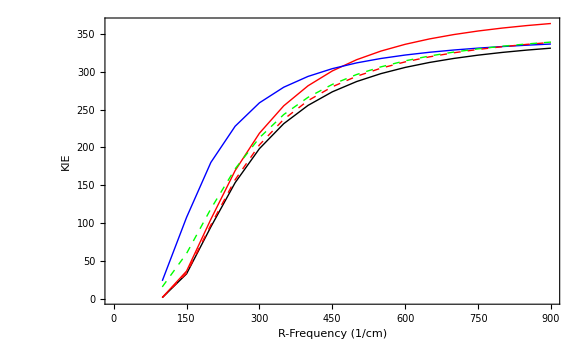

```mathematica
nn=2;mm=2;
TT=303;ΔΔ=-5;λλ=20;RR=R0[2.7];μμ=100;
start=100;finish=900;step=50;
Monitor[
ListLinePlot[
{Tooltip[Table[{ω,KIEqflux[TT,ΔΔ,λλ,RR,μμ,ω,nn,mm]},{ω,start,finish,step}],"qflux"],
Tooltip[Table[{ω,KIE6[TT,ΔΔ,λλ,RR,μμ,ω,nn,mm]},{ω,start,finish,step}],"High-T"],
Tooltip[Table[{ω,KIElowT[TT,ΔΔ,λλ,RR,μμ,ω,nn,mm]},{ω,start,finish,step}],"Low-T"],
Tooltip[Table[{ω,KIE7[TT,ΔΔ,λλ,RR,μμ,ω,nn,mm]},{ω,start,finish,step}],"High-T (λ_α=0)"],
Tooltip[Table[{ω,KIEUK[TT,ΔΔ,λλ,RR,μμ,ω,nn,mm]},{ω,start,finish,step}],"High-T (UK)"]},PlotStyle->{Black,Red,Blue,{Red,Dashed},{Green,Dashed}},Frame->True,Axes->False,FrameLabel->{"R-Frequency (1/cm)","KIE","Mass = 100 amu; λ=20 kcal/mol"},InterpolationOrder->4],{"Frequency"->ω,ProgressIndicator[Dynamic[ω],{start,finish}]}]
```

#### Rates vs. reaction free energy

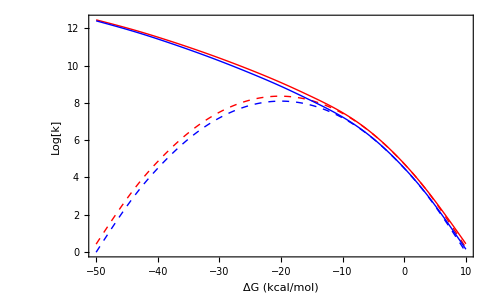

```mathematica
nn=6;mm=6;
TT=303;λλ=20;RR=R0[2.7];μμ=100;ωω=200;
start=-50;finish=10;step=5;
Monitor[
ListLinePlot[
{Tooltip[Table[{dg,Log[10,TotalrateH6[TT,dg,λλ,RR,μμ,ωω,0,0]]},{dg,start,finish,step}],"High-T RateH(6) (0-0)"],Tooltip[Table[{dg,Log[10,TotalrateH6[TT,dg,λλ,RR,μμ,ωω,nn,mm]]},{dg,start,finish,step}],"High-T RateH(6) (0-0)"],Tooltip[Table[{dg,Log[10,TotalratelowH[TT,dg,λλ,RR,μμ,ωω,0,0]]},{dg,start,finish,step}],"Low-T RateH"],Tooltip[Table[{dg,Log[10,TotalratelowH[TT,dg,λλ,RR,μμ,ωω,nn,mm]]},{dg,start,finish,step}],"Low-T RateH"]},
PlotStyle->{{Red,Dashed},Red,{Blue,Dashed},Blue},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","Log[k]"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```

#### Channel contributions vs. reaction free energy

Parameter description:
Grange={Δ1,Δ2,δ} - (list) range of ΔG: from Δ1 to Δ2 with stepsize δ (i.e. (1+(Δ2-Δ1)/δ) points will be plotted);
n, m - highest quantum number for reactant and product states required for convergence in the whole range of ΔG's;
nout, mout - highest quantum number of reactant and product states for which the contributions will be plotted.

```mathematica
qfluxcontributions[T_,Grange_,λ_,R_,μ_,ω_,n_,m_,nout_,mout_]:=
Module[{dG,Δ1, Δ2, δ,Hmatrixlist,Dmatrixlist,i,j},
{Δ1,Δ2,δ}=Grange;
Monitor[Hmatrixlist=Table[rateqfluxHmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Hydrogen: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
Monitor[Dmatrixlist=Table[rateqfluxDmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Deuterium: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
ListLinePlot[Join[Flatten[Table[Tooltip[Hmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(H)"],{i,1,nout+1},{j,1,mout+1}],1],Flatten[Table[Tooltip[Dmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(D)"],{i,1,nout+1},{j,1,mout+1}],1]],Frame->True,Axes->False,DataRange->{Δ1,Δ2},FrameLabel->{"ΔG (kcal/mol)","channel contribution (%)"},PlotRange->All,InterpolationOrder->4]
];
```

```mathematica
rate6contributions[T_,Grange_,λ_,R_,μ_,ω_,n_,m_,nout_,mout_]:=
Module[{dG,Δ1,Δ2,δ,Hmatrixlist,Dmatrixlist,i,j},
{Δ1,Δ2,δ}=Grange;
Monitor[Hmatrixlist=Table[rateH6matrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Hydrogen: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
Monitor[Dmatrixlist=Table[rateD6matrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Deuterium: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
ListLinePlot[Join[Flatten[Table[Tooltip[Hmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(H)"],{i,1,nout+1},{j,1,mout+1}],1],Flatten[Table[Tooltip[Dmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(D)"],{i,1,nout+1},{j,1,mout+1}],1]],Frame->True,Axes->False,DataRange->{Δ1,Δ2},FrameLabel->{"ΔG (kcal/mol)","channel contribution (%)"},PlotRange->All,InterpolationOrder->4]
];
```

```mathematica
rate7contributions[T_,Grange_,λ_,R_,μ_,ω_,n_,m_,nout_,mout_]:=
Module[{dG,Δ1,Δ2,δ,Hmatrixlist,Dmatrixlist,i,j},
{Δ1,Δ2,δ}=Grange;
Monitor[Hmatrixlist=Table[rateH7matrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Hydrogen: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
Monitor[Dmatrixlist=Table[rateD7matrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Deuterium: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
ListLinePlot[Join[Flatten[Table[Tooltip[Hmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(H)"],{i,1,nout+1},{j,1,mout+1}],1],Flatten[Table[Tooltip[Dmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(D)"],{i,1,nout+1},{j,1,mout+1}],1]],Frame->True,Axes->False,DataRange->{Δ1,Δ2},FrameLabel->{"ΔG (kcal/mol)","channel contribution (%)"},PlotRange->All,InterpolationOrder->4]
];
```

```mathematica
lowTcontributions[T_,Grange_,λ_,R_,μ_,ω_,n_,m_,nout_,mout_]:=
Module[{dG,Δ1,Δ2,δ,Hmatrixlist,Dmatrixlist,i,j},
{Δ1,Δ2,δ}=Grange;
Monitor[Hmatrixlist=Table[ratelowHmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Hydrogen: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
Monitor[Dmatrixlist=Table[ratelowDmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Deuterium: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
ListLinePlot[Join[Flatten[Table[Tooltip[Hmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(H)"],{i,1,nout+1},{j,1,mout+1}],1],Flatten[Table[Tooltip[Dmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(D)"],{i,1,nout+1},{j,1,mout+1}],1]],Frame->True,Axes->False,DataRange->{Δ1,Δ2},FrameLabel->{"ΔG (kcal/mol)","channel contribution (%)"},PlotRange->All,InterpolationOrder->4]
];
```

```mathematica
UKcontributions[T_,Grange_,λ_,R_,μ_,ω_,n_,m_,nout_,mout_]:=
Module[{dG,Δ1,Δ2,δ,Hmatrixlist,Dmatrixlist,i,j},
{Δ1,Δ2,δ}=Grange;
Monitor[Hmatrixlist=Table[rateUKHmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Hydrogen: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
Monitor[Dmatrixlist=Table[rateUKDmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Deuterium: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
ListLinePlot[Join[Flatten[Table[Tooltip[Hmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(H)"],{i,1,nout+1},{j,1,mout+1}],1],Flatten[Table[Tooltip[Dmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(D)"],{i,1,nout+1},{j,1,mout+1}],1]],Frame->True,Axes->False,DataRange->{Δ1,Δ2},FrameLabel->{"ΔG (kcal/mol)","channel contribution (%)"},PlotRange->All,InterpolationOrder->4]
];
```

```mathematica
UKqcontributions[T_,Grange_,λ_,R_,μ_,ω_,n_,m_,nout_,mout_]:=
Module[{dG,Δ1,Δ2,δ,Hmatrixlist,Dmatrixlist,i,j},
{Δ1,Δ2,δ}=Grange;
Monitor[Hmatrixlist=Table[rateUKqHmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Hydrogen: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
Monitor[Dmatrixlist=Table[rateUKqDmatrix[T,dG,λ,R,μ,ω,n,m],{dG,Δ1,Δ2,δ}],{"Deuterium: ΔG"->dG,ProgressIndicator[Dynamic[dG],{Δ1,Δ2}]}];
ListLinePlot[Join[Flatten[Table[Tooltip[Hmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(H)"],{i,1,nout+1},{j,1,mout+1}],1],Flatten[Table[Tooltip[Dmatrixlist⟦All,i,j⟧,ToString[i-1]<>"->"<>ToString[j-1]<>"(D)"],{i,1,nout+1},{j,1,mout+1}],1]],Frame->True,Axes->False,DataRange->{Δ1,Δ2},FrameLabel->{"ΔG (kcal/mol)","channel contribution (%)"},PlotRange->All,InterpolationOrder->4]
];
```

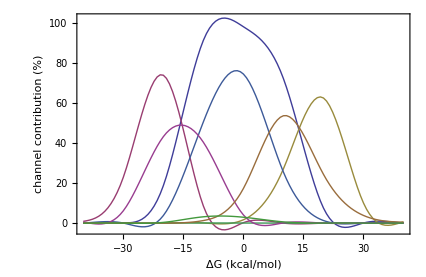

```mathematica
rate6contributions[303,{-40,40,10},20,R0[2.7],100,200,2,2,1,1]
```

#### KIE vs. reaction free energy

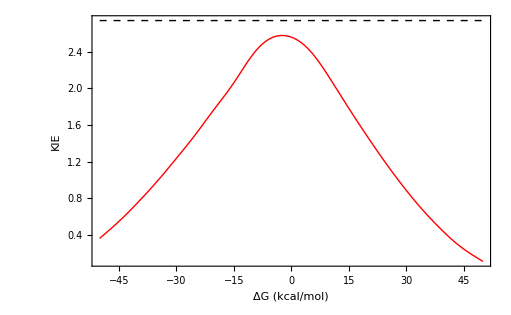

```mathematica
nn=15;mm=15;
TT=303;λλ=20;RR=R0[2.7];μμ=100;ωω=200;
start=-70;finish=70;step=10;
Monitor[
ListLinePlot[
{Table[{dg,Log[10,KIERT[TT,dg,λλ,RR,μμ,ωω,0,0]]},{dg,start,finish,step}],
Table[{dg,Log[10,KIERT[TT,dg,λλ,RR,μμ,ωω,nn,mm]]},{dg,start,finish,step}]},
PlotStyle->{{Black,Dashed},Red},Frame->True,Axes->False,
FrameLabel->{"ΔG (kcal/mol)","KIE"},
PlotRange->All,InterpolationOrder->4],
{"ΔG"->dg,ProgressIndicator[Dynamic[dg],{start,finish}]}]
```